```mathematica
ClearAll["Global`*"]
```

```mathematica
Sol=Solve[{rh*H*(1-(H+ahm*M)/kh)==0,rm*M*(1-(M+amh*H)/km)==0},{H,M}]
```

{{H→0,M→km},{H→-(kh-ahm km)/(-1+ahm amh),M→-(-amh kh+km)/(-1+ahm amh)},{H→0,M→0},{H→kh,M→0}}

D-differentiation... soma will influence the germ line... germ cells will incorporate aspects of the soma.

World Population from 1800 to now

WolframAlphaQueryResults

```mathematica
TS=WolframAlpha["World Population from 1800 to now",{{"SensiblePlot:Population:CountryData",1},"FormattedData"}];
data=Delete[TS[[1]][[1,All,2]],1];
data = Delete[data,Table[{i},{i,1,16}]];
```

```mathematica
(*Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/math/data.dat",data];*)
```

```mathematica
data = Flatten[Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/math/data.dat"],1];
```

```mathematica
data
```

{1.01519,1.0196,1.02402,1.02844,1.03289,1.04042,1.04807,1.0558,1.06374,1.07172,1.07951,1.08731,1.09519,1.1042,1.11332,1.11825,1.12308,1.12788,1.1326,1.13819,1.14377,1.14934,1.15527,1.16113,1.16706,1.17234,1.17772,1.1831,1.18859,1.19418,1.1997,1.20545,1.21081,1.21642,1.22222,1.22314,1.22437,1.22707,1.22982,1.23252,1.23535,1.23889,1.24213,1.24594,1.24982,1.25442,1.25782,1.26252,1.26664,1.27096,1.27507,1.27936,1.28415,1.28973,1.29454,1.3041,1.31308,1.3224,1.332,1.34305,1.35174,1.36299,1.37291,1.38232,1.39238,1.4033,1.41357,1.42435,1.43523,1.44633,1.45656,1.46719,1.4779,1.48891,1.50015,1.51123,1.52259,1.5343,1.54651,1.55859,1.56995,1.58305,1.59565,1.60838,1.62213,1.63426,1.64836,1.65931,1.66993,1.68118,1.69166,1.70325,1.71541,1.72705,1.73973,1.75433,1.76818,1.78183,1.7948,1.80717,1.81933,1.83066,1.83914,1.8462,1.863,1.8777,1.8955,1.91341,1.93141,1.94955,1.96526,1.9823,2.0022,2.02117,2.04218,2.06252,2.08547,2.10693,2.12708,2.14843,2.16973,2.19175,2.21398,2.23624,2.25517,2.2733,2.29303,2.31105,2.33046,2.35258,2.37847,2.40986,2.44143,2.47313,2.51679,2.55959,2.60516,2.65191,2.70184,2.75663,2.80276,2.85836,2.91433,2.9725,3.03284,3.09419,3.16074,3.22435,3.28876,3.35431,3.41662,3.48201,3.54795,3.61517,3.69619,3.77205,3.84832,3.92467,4.00076,4.07642,4.15141,4.22586,4.3004,4.3759,4.45301,4.5318,4.61212,4.6941,4.77783,4.86329,4.95059,5.03948,5.12911,5.21837,5.30643,5.39294,5.47801,5.56174,5.64442,5.72624,5.80721,5.88726,5.96646,6.04493,6.12277,6.2,6.27672,6.3532,6.42976,6.50665,6.58396,6.66164,6.73961,6.81774,6.89589,6.97404,7.05214}

```mathematica
diffdata = Differences[data];
```

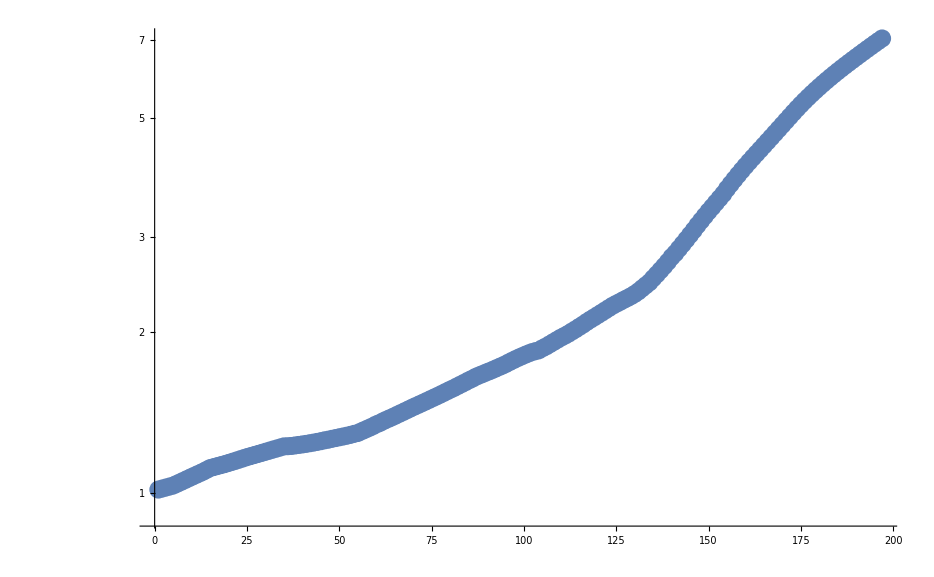

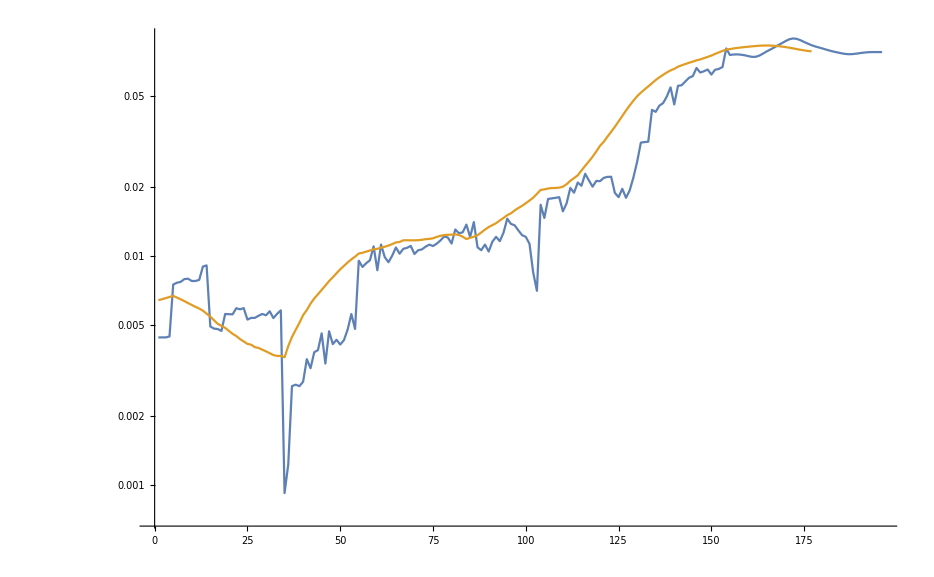

0.00722552

```mathematica
ListLogPlot[data]
ListLogPlot[{diffdata,MovingAverage[diffdata,20]},Joined->True]
Mean[diffdata[[1;;84]]]
```

```mathematica
data[[1]]
```

1.01519

The world without monsters...
Humans start at 1.02x10^9 people in 1816 and end with 7.18x10^9 people today
In our model, the growth rate needs to be at 0.008-0.01 or so to achieve this...

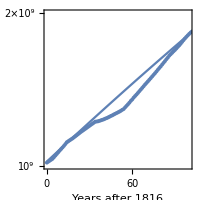

```mathematica
CompDyn[rh_,ahm_,kh_,rm_,amh_,km_,T_] :=

NDSolve[{
H'[t] ==rh*H[t]*(1-(H[t]+ahm*M[t])/kh),
M'[t] ==rm*M[t]*(1-(M[t]+amh*H[t])/km),
H[0]==1.02*10^9,M[0]==0},{H,M},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{rh=0.0067,rm=0.01,ahm=5,amh=0.1,kh=10*10^9,km=10*10^6,T=200},
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh,ahm,kh,rm,amh,km,T] ];
Show[{
LogPlot[Traj,{t,0,T/2},PlotRange->{1*10^9,2*10^9},AspectRatio->1,Frame->True,FrameLabel->{"Years after 1816","Human population"}],
ListLogPlot[Transpose[{Table[i,{i,0,Length[data]-1}],data*10^9}],Joined->False,PlotStyle->Dashed]
},ImageSize->200]
]
```

Dynamics with monster population

Last::nolast: {} has a length of zero and no last element.

Import::chtype: First argument "\"\"" is not a valid file, directory, or URL specification.

Last::nolast: {} has a length of zero and no last element.

Import::chtype: First argument "\"\"" is not a valid file, directory, or URL specification.

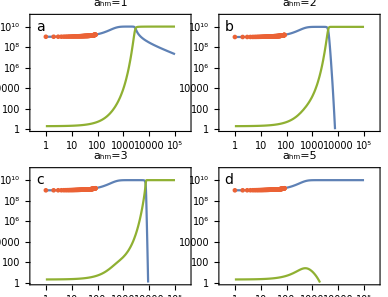
-Graphics-Human populationYears after 1816

```mathematica
CompDyn[rh_,rm_,ahm_,c_,k_,T_] :=

NDSolve[{
H'[t] ==rh*H[t]*(1-(H[t]+ahm*M[t])/k),
M'[t] ==rm*M[t]*(1-(M[t]+ahm/c*H[t])/k),
H[1]==1.02*10^9,M[1]==2},{H,M},{t,1,T},MaxSteps->Infinity,InterpolationOrder->All];

xaxes={Automatic,Automatic,Automatic,Automatic};
yaxes = {Automatic, Automatic, Automatic,Automatic};
size = {300,285,330,325};
letter = {Style["a",FontSize->14],Style["b",FontSize->14],Style["c",FontSize->14],Style["d",FontSize->14]};
TrajAMb = Import["","table"];
TrajAMc = Import["","table"];
PlotTraj=Labeled[
GraphicsGrid[
ArrayReshape[
tic=0;
Table[
tic = tic+1;
With[{rh=0.0067,rm=0.0067*1.5,ahm=AHM,c=4,k=10*10^9,T=10^5},
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh,rm,ahm,c,k,T] ];
Show[{
LogLogPlot[Traj,{t,1,T},PlotRange->{1,All},AspectRatio->0.67,PlotStyle->{ColorData[97,1],ColorData[97,3]},Frame->True,FrameLabel->{None,None},FrameTicks->{xaxes[[tic]],yaxes[[tic]]},PlotRangePadding->0.2,PlotLabel->StringJoin[{"a_hm=",ToString[AHM]}]],
ListLogLogPlot[Transpose[{Table[i,{i,0,84}],data[[1;;85]]*10^9}],Joined->False,PlotStyle->ColorData[97,4]],
Graphics[Text[letter[[tic]],{Log@0.6,Log@(10^10)}]]
},ImageSize->200]
],{AHM,{1,2,3,5}}],{2,2}]
,Spacings->{{-40,-10}}],
TraditionalForm/@{Rotate["Human population",90Degree],"Years after 1816"},{Left,Bottom},Spacings->{0,0},LabelStyle->"Panel"]
```

```mathematica
Table[i,{i,{{1,2},{3,4}}}]
```

{{1,2},{3,4}}

```mathematica
Flatten
```

Flatten

```mathematica
if1=CompDyn[rh->0.0067,rm->0.0067,ahm->1,amh->0,k->10*10^9,T->10000][[1,All,-1]]
```

NDSolve::ndnl: Endpoint T → 10000. in {t, 0., T → 10000.} is not a real number.

{H[t] (rh→0.0067) (1-(H[t]+M[t] (rm→0.0067))/(k→10000000000)),M[t] (ahm→1) (1-(M[t]+H[t] (amh→0))/(k→10000000000)),1.02×10^9,1}

{{                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t],                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t]}}

```mathematica
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh=0.0067,ahm=1,rm=0.0067,amh=0,k=10*10^9,T=10^10] ]
```

{{                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t],                                 10
InterpolatingFunction[{{0., 1. 10  }}, <>][t]}}

```mathematica
Traj[[1]][[1]]/.t->10^(9)
```

1492.54

```mathematica
cvalues={2,4,6,8,10};
PET=ParallelTable[
Traj=Evaluate[{H[t],M[t]}/.CompDyn[rh=0.0067,ahm=AHM,rm=0.0067,amh=AHM/c,k=10*10^9,T=10^10] ];
ET=
Table[
time = 10^i;
size=Traj[[1]][[1]]/.t->time;
ext=0;
If[size < 1000,
ext=1;
Return[ time,Table]
],
{i,0,10,0.01}
];
If[ext ==1,
TExt = ET,
TExt = Infinity
];
{AHM,TExt},
{AHM,0.01,10,0.01},{c,cvalues}
];
```

```mathematica
MinExt = Select[PET,#[[2]]==Min[PET[[All,2]]]&]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

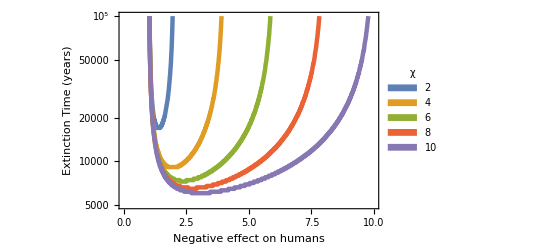

```mathematica
ExtTimePlot=
ListLogPlot[Table[PET[[All,i]],{i,1,5}],PlotRange->{5000,10^5},PlotStyle->Thickness[.008],Frame->True,FrameLabel->{"Negative effect on humans","Extinction Time (years)"},Joined->True,PlotLegends->SwatchLegend[Automatic,cvalues,LegendLabel->"χ"]]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_ExtTime.pdf",ExtTimePlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_ExtTime.pdf

```mathematica
Remove[t]
```

Can we calculate the extinction time as a function of amh and ahm assuming that kh, km, rm, rh are set?

```mathematica
Table[PET[[All,i]],{i,1,6}]
```

Part::partw: Part 6 of {{0.01, ∞}, {0.01, ∞}, {0.01, ∞}, {0.01, ∞}, {0.01, ∞}} does not exist.

{{{0.01,∞},{0.01,∞},{0.01,∞},{0.01,∞},{0.01,∞}},{{0.015,∞},{0.015,∞},{0.015,∞},{0.015,∞},{0.015,∞}},{{0.02,∞},{0.02,∞},{0.02,∞},{0.02,∞},{0.02,∞}},1993,{{9.99,∞},{9.99,∞},{9.99,∞},{9.99,∞},{9.99,1.77828×10^6}},{{9.995,∞},{9.995,∞},{9.995,∞},{9.995,∞},{9.995,3.54813×10^6}},{{10.,∞},{10.,∞},{10.,∞},{10.,∞},{10.,∞}}}⟦All,6⟧
 |  |  |  |

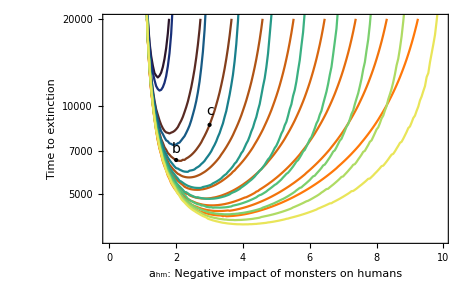

```mathematica
tExt=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_text_lowdeath.csv","table"];
tExtAM=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_textam2_lowdeath.csv","table"];
tExtAMLarge=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_textamklarge.csv","table"];
tExtAMSmall=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_textamksmall.csv","table"];
PAll = Show[{ColorData["RustTones","Image"]},AspectRatio->1];
PAM=Show[{ColorData["BlueGreenYellow","Image"]},AspectRatio->1];
valuesC4=Transpose[{Table[j,{j,1,10,0.05}],tExt[[All,4]]}];
PlotAMExt=Show[{
ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExt[[All,i]]}],{i,1,Length[tExt[[1,All]]]}],Joined->True,PlotStyle->"RustTones",PlotRange->{3500,2*10^4},Frame->True,FrameLabel->{"a_hm: Negative impact of monsters on humans","Time to extinction"},
PlotLegends->Placed[SwatchLegend[{"Global","Amazon catalyst"},LegendMarkers->{PAll,PAM}],{ 0.8,0.15}]],
ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExtAM[[All,i]]}],{i,1,Length[tExt[[1,All]]]}],Joined->True,PlotStyle->"BlueGreenYellow"],
(*ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExtAMSmall[[All,i]]}],{i,1,Length[tExtAMSmall[[1,All]]]}],Joined->True,PlotStyle->"BlueGreenYellow",ColorFunction->(Directive[Opacity[0.5]])],*)
(*ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExtAMLarge[[All,i]]}],{i,1,Length[tExtAMLarge[[1,All]]]}],Joined->True,PlotStyle->"BlueGreenYellow",ColorFunction->(Directive[Opacity[0.5]])],*)
(*Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==1&][[1]][[1]],Log@Select[valuesC4,#[[1]]==1&][[1]][[2]]}]
}],*)
Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==2&][[1]][[1]],Log@Select[valuesC4,#[[1]]==2&][[1]][[2]]}]
}],
Graphics[
Text[Style["b",FontSize->14],{Select[valuesC4,#[[1]]==2&][[1]][[1]],Log@(Select[valuesC4,#[[1]]==2&][[1]][[2]]+600)}]
],
Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==3&][[1]][[1]],Log@Select[valuesC4,#[[1]]==3&][[1]][[2]]}]
}],
Graphics[
Text[Style["c",FontSize->14],{Select[valuesC4,#[[1]]==3&][[1]][[1]],Log@(Select[valuesC4,#[[1]]==3&][[1]][[2]]+1000)}]
]
(*,
Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==5&][[1]][[1]],Log@Select[valuesC4,#[[1]]==5&][[1]][[2]]}]
}]*)
},ImageSize->400]
```

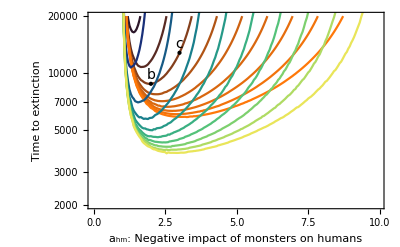

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_AmExt.pdf",PlotAMExt,"PDF"]
```

```mathematica
{Select[valuesC4,#[[1]]==2&][[1]][[1]],Log@Select[valuesC4,#[[1]]==2&][[1]][[1]]}
```

{2.,0.693147}

```mathematica
valuesC4=Transpose[{Table[j,{j,1,10,0.05}],tExt[[All,4]]}]
```

{{1.,Inf},{1.05,45076.5},{1.1,26063.4},{1.15,19344.2},{1.2,15801.4},{1.25,13841.},{1.3,12492.5},{1.35,11564.1},{1.4,10825.7},{1.45,10389.9},{1.5,9943.38},{1.55,9602.75},{1.6,9372.91},{1.65,9173.16},{1.7,9077.5},{1.75,8955.75},{1.8,8864.74},{1.85,8807.47},{1.9,8771.31},{1.95,8753.3},{2.,8762.31},{2.05,8782.66},{2.1,8826.45},{2.15,8876.37},{2.2,8989.04},{2.25,9075.94},{2.3,9176.73},{2.35,9293.84},{2.4,9432.31},{2.45,9567.78},{2.5,9748.39},{2.55,9931.2},{2.6,10163.3},{2.65,10388.7},{2.7,10638.},{2.75,10912.1},{2.8,11222.3},{2.85,11551.9},{2.9,11914.8},{2.95,12318.8},{3.,12788.8},{3.05,13286.},{3.1,13837.5},{3.15,14477.5},{3.2,15180.7},{3.25,15975.1},{3.3,16902.7},{3.35,17964.3},{3.4,19184.2},{3.45,20641.2},{3.5,22368.7},{3.55,24487.3},{3.6,27100.1},{3.65,30438.},{3.7,34859.1},{3.75,40987.7},{3.8,50040.8},{3.85,64888.8},{3.9,93840.7},{3.95,177196.},{4.,Inf},{4.05,Inf},{4.1,Inf},{4.15,Inf},{4.2,Inf},{4.25,Inf},{4.3,Inf},{4.35,Inf},{4.4,Inf},{4.45,Inf},{4.5,Inf},{4.55,Inf},{4.6,Inf},{4.65,Inf},{4.7,Inf},{4.75,Inf},{4.8,Inf},{4.85,Inf},{4.9,Inf},{4.95,Inf},{5.,Inf},{5.05,Inf},{5.1,Inf},{5.15,Inf},{5.2,Inf},{5.25,Inf},{5.3,Inf},{5.35,Inf},{5.4,Inf},{5.45,Inf},{5.5,Inf},{5.55,Inf},{5.6,Inf},{5.65,Inf},{5.7,Inf},{5.75,Inf},{5.8,Inf},{5.85,Inf},{5.9,Inf},{5.95,Inf},{6.,Inf},{6.05,Inf},{6.1,Inf},{6.15,Inf},{6.2,Inf},{6.25,Inf},{6.3,Inf},{6.35,Inf},{6.4,Inf},{6.45,Inf},{6.5,Inf},{6.55,Inf},{6.6,Inf},{6.65,Inf},{6.7,Inf},{6.75,Inf},{6.8,Inf},{6.85,Inf},{6.9,Inf},{6.95,Inf},{7.,Inf},{7.05,Inf},{7.1,Inf},{7.15,Inf},{7.2,Inf},{7.25,Inf},{7.3,Inf},{7.35,Inf},{7.4,Inf},{7.45,Inf},{7.5,Inf},{7.55,Inf},{7.6,Inf},{7.65,Inf},{7.7,Inf},{7.75,Inf},{7.8,Inf},{7.85,Inf},{7.9,Inf},{7.95,Inf},{8.,Inf},{8.05,Inf},{8.1,Inf},{8.15,Inf},{8.2,Inf},{8.25,Inf},{8.3,Inf},{8.35,Inf},{8.4,Inf},{8.45,Inf},{8.5,Inf},{8.55,Inf},{8.6,Inf},{8.65,Inf},{8.7,Inf},{8.75,Inf},{8.8,Inf},{8.85,Inf},{8.9,Inf},{8.95,Inf},{9.,Inf},{9.05,Inf},{9.1,Inf},{9.15,Inf},{9.2,Inf},{9.25,Inf},{9.3,Inf},{9.35,Inf},{9.4,Inf},{9.45,Inf},{9.5,Inf},{9.55,Inf},{9.6,Inf},{9.65,Inf},{9.7,Inf},{9.75,Inf},{9.8,Inf},{9.85,Inf},{9.9,Inf},{9.95,Inf},{10.,Inf}}

```mathematica
valuesC4[[All,1]]
```

{1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.,5.05,5.1,5.15,5.2,5.25,5.3,5.35,5.4,5.45,5.5,5.55,5.6,5.65,5.7,5.75,5.8,5.85,5.9,5.95,6.,6.05,6.1,6.15,6.2,6.25,6.3,6.35,6.4,6.45,6.5,6.55,6.6,6.65,6.7,6.75,6.8,6.85,6.9,6.95,7.,7.05,7.1,7.15,7.2,7.25,7.3,7.35,7.4,7.45,7.5,7.55,7.6,7.65,7.7,7.75,7.8,7.85,7.9,7.95,8.,8.05,8.1,8.15,8.2,8.25,8.3,8.35,8.4,8.45,8.5,8.55,8.6,8.65,8.7,8.75,8.8,8.85,8.9,8.95,9.,9.05,9.1,9.15,9.2,9.25,9.3,9.35,9.4,9.45,9.5,9.55,9.6,9.65,9.7,9.75,9.8,9.85,9.9,9.95,10.}

```mathematica
{Select[valuesC4,#[[1]]==2&][[1]][[1]],Log@Select[valuesC4,#[[1]]==2&][[1]][[1]]}
```

{2.,0.693147}

```mathematica
CombinedPlot =GraphicsGrid[{{PlotAMExt,PlotTraj}},ImageSize->900,Spacings->10]
```

-Graphics-

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_combined.pdf",CombinedPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_combined.pdf

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_combined.pdf",%716,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_combined.pdf

```mathematica
ColorData["BlueGreenYellow"]
```

ColorDataFunction[…]

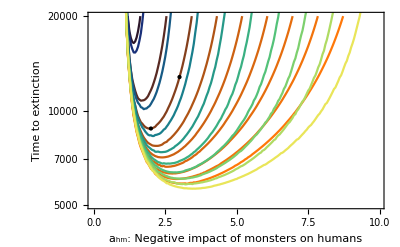

```mathematica
tExt=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_text.csv","table"];
tExtAM=Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_textam2.csv","table"];
PAll = Show[{ColorData["RustTones","Image"]},AspectRatio->1];
PAM=Show[{ColorData["BlueGreenYellow","Image"]},AspectRatio->1];
valuesC4=Transpose[{Table[j,{j,1,10,0.05}],tExt[[All,4]]}];
PlotAMExtKLARGE=Show[{
ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExt[[All,i]]}],{i,1,Length[tExt[[1,All]]]}],Joined->True,PlotStyle->"RustTones",PlotRange->{5000,2*10^4},Frame->True,FrameLabel->{"a_hm: Negative impact of monsters on humans","Time to extinction"},
PlotLegends->Placed[SwatchLegend[{"Global","Amazon catalyst"},LegendMarkers->{PAll,PAM}],{ 0.8,0.15}]],
ListLogPlot[Table[Transpose[{Table[j,{j,1,10,0.05}],tExtAM[[All,i]]}],{i,1,Length[tExt[[1,All]]]}],Joined->True,PlotStyle->"BlueGreenYellow"],
(*Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==1&][[1]][[1]],Log@Select[valuesC4,#[[1]]==1&][[1]][[2]]}]
}],*)
Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==2&][[1]][[1]],Log@Select[valuesC4,#[[1]]==2&][[1]][[2]]}]
}],
Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==3&][[1]][[1]],Log@Select[valuesC4,#[[1]]==3&][[1]][[2]]}]
}](*,
Graphics[{PointSize[Large],
Point[{Select[valuesC4,#[[1]]==5&][[1]][[1]],Log@Select[valuesC4,#[[1]]==5&][[1]][[2]]}]
}]*)
},ImageSize->400]
```